# Linear Transformations To Render 3D Graphics

Rendering of graphics on screen is connected to (not surprisingly) maths, this essay gives a some intuition about it.

Harshal Gajjar, Jun. 28,  2018

## Getting started with Projections

Imagine a soccer ball on street at noon on a sunny day.

```mathematica
Show[Graphics3D[Style[Sphere[{0,0,1},1],Gray]],
Plot3D[0,{x,y}∈Disk[{0,0},1],PlotStyle->Gray,Mesh->False],Axes->True, AxesLabel->{x,y,z}]
```

-Graphics3D-

Think about the shadow that it casts on the street.
There’s a way of “creating” the shadow of the soccer ball on the street - by dropping all the points on the surface of the ball onto the street!

Let' s imagine that the axes are as shown in the figure above - street on XY plane and Z axis perpendicular to the plane.

This dropping (projection) of points (x,y,z) from the surface of the sphere (x^2+y^2+(z-1)^2==1) onto the XY plane can be represented as multiplying a matrix (let’s call it “toPlane”) with a point, like so:

```mathematica
point = {x,y,z};
toPlane = ({{1, 0, 0}, {0, 1, 0}});
```

```mathematica
toPlane . point
```

{x,y}

Once every point has been projected onto the XY plane (street), the projection would actually represent the top view of that sphere.

Let’s take another example, rotate the cylinder below to view it from top:

```mathematica
Show[Graphics3D[Cylinder[{{0,0,0.40},{1,1,1.40}},1/2]],
	 Plot3D[0, {x,y}∈Disk[{0,0},2], PlotStyle->Gray,Mesh->False], 
	 Axes->True, AxesLabel->{x,y,z}, ViewPoint->{0,-15,0}]
```

-Graphics3D-

This is what you should see, which is a projection of the cylinder on the XY plane (street):

```mathematica
Show[Graphics3D[Cylinder[{{0,0,0},{1,1,1}},1/2]],
	Axes->True, AxesLabel->{x,y,z}, ViewPoint->{0,0,20},
	Method->{"RotationControl"->None}]
```

-Graphics3D-

But of course shadows aren’t coloured so this is what the shadow would look like:

```mathematica
Show[Graphics3D[Cylinder[{{0,0,0},{1,1,1}},1/2], Boxed->False],
	Axes->{True,True,False}, AxesLabel->{x,y,""}, Lighting->None,
	ViewPoint->{0,0,20}, Method->{"RotationControl"->None}]
```

-Graphics3D-

Now, we have a way of producing top views of objects: multiply the points on the surface of the object with the matrix (“toPlane”) and then plot those points on a 2D surface and then show the plot on the 2D sheet of paper.

Important thing to notice here is that since the screens are two dimensional it’s extremely easy for the computer to show two dimensional plots, just like it’s easy for us to plot something on a piece of paper. A computer can, for instance, achieve this by placing the origin at the bottom left corner of the screen and considering each pixel as a unit on the two axes - X and Y.

## Changing Perspective

As you saw from above (pun intended), multiplying with a matrix gave points to be plotted on a 2D plane which would represent the top view of the object.

Let’s now create some other view, but this time of a cone (x^2+y^2=z^2). 
Feel free to experiment with f, maybe replace “cone” with “cylinder” .

Creating a list of (some) points on the surface of the cone, verify that all points lie on a cone by rotating the graphic below:

```mathematica
cone[θ_,z_]:={Sqrt[(z^2)]*Cos[θ],Sqrt[(z^2)]*Sin[θ],z}
cylinder[θ_,z_]:={Cos[θ],Sin[θ],z}

f[θ_,z_]:=cone[θ,z];
points=Flatten[Table[f[θ,z], {θ,-Pi,Pi,0.05}, {z,0,+0.5,0.05}], 1];
"Points: "Short[points,5]

ListPointPlot3D[points, PlotRange->{{-1,1},{-1,1},{-1,1}}, BoxRatios->1, AxesLabel->{x,y,z}]
```

Points:  {{0.,0.,0.},{-0.05,-6.12323×10^-18,0.05},{-0.1,-1.22465×10^-17,0.1},{-0.15,-1.83697×10^-17,0.15},«1379»,{-0.39978,0.0132717,0.4},{-0.449752,0.0149306,0.45},{-0.499725,0.0165896,0.5}}

-Graphics3D-

Let us rotate the cylinder by an angle α around the x axis (following right hand rule):

```mathematica
α = 0;
{"α "Slider[Dynamic[α],{0,2*Pi,0.2}],Dynamic[α]}
```

{α  ,}

Let's call this new matrix for rotating - "rotateX". 
We’ll also define a function ToPlane, which projects a point (x,y,z) onto XY plane (x,y).

```mathematica
rotateX=({{1, 0, 0}, {0, Cos[α], -Sin[α]}, {0, Sin[α], Cos[α]}});
ToPlane[x_]:=(toPlane.x);
```

Now, let’s create a function for matrix multiplication, which takes in a point (x,y,z) and gives the location of same point after rotation by multiplying it with rotateX.

```mathematica
RotateX[x_]:=({{1, 0, 0}, {0, Cos[α], -Sin[α]}, {0, Sin[α], Cos[α]}}).x;
```

And let’s rotate! Move the slider (to change α) and see the rotation in action.
Remeber, after rotation we also project all the points onto XY plane (in order to plot it on a 2D plane) by using the function we defined - ToPlane[x]

```mathematica
Dynamic[ListPlot[Map[ToPlane, Map[RotateX, Map[RotateY, Map[RotateZ,points]]]],
				PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1, 
				PlotLabel->"3D points projected onto 2D plane"]]
```

Let’s define a two more matrices to rotate around  y and z axes at angles β and γ respectively:

```mathematica
β = 0; γ = 0;
{"α "Slider[Dynamic[α],{0,2*Pi,0.2}],Dynamic[α]}
{"β "Slider[Dynamic[β],{0,2*Pi,0.2}],Dynamic[β]}
{"γ "Slider[Dynamic[γ],{0,2*Pi,0.2}],Dynamic[γ]}
RotateY[x_]:=({{Cos[β], 0, Sin[β]}, {0, 1, 0}, {-Sin[β], 0, Cos[β]}}).x;
RotateZ[x_]:=({{Cos[γ], -Sin[γ], 0}, {Sin[γ], Cos[γ], 0}, {0, 0, 1}}).x;
```

{α  ,}

{β  ,}

{γ  ,}

This is where the cone is in 3D, verify that it is indeed rotating about the axes by interacting with the graphic below:

```mathematica
Dynamic[ListPointPlot3D[Map[RotateX, Map[RotateY, Map[RotateZ,points]]],
		PlotRange->{{-1,1},{-1,1},{-1,1}}, 
		ViewPoint->{0, -1, 10}, BoxRatios->1, AxesLabel->{x, y, z}, PlotLabel->"Plotted in 3D"]]
```

There are also matrices that do other operations like scaling:

```mathematica
scale[factor_,x_]:=({{factor, 0, 0}, {0, factor, 0}, {0, 0, factor}}).x;
```

So, something happens on your screen - there’s a matrix multiplication that’s making it possible!

## Further explorations

Coding the Matrix: https://books.google.com/books/about/Coding_the_Matrix.html?id=8PmPngEACAAJ&hl=en

Linear Algebra wiki: https://en.wikipedia.org/wiki/Linear_algebra

Introduction to Computer Graphics: https://cs.brown.edu/courses/cs123/docs/helpsessions/linearalgebra.pdf

## Author Information

Harshal Gajjar
28^th June 2018
Boston, MA
gotoharshal@gmail.com

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

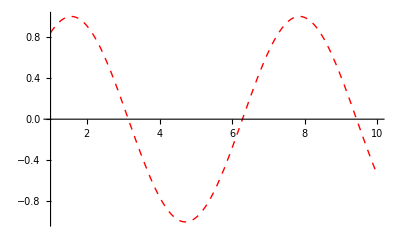

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

-Graphics-

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)